### Programa para leer datos .txt obtenidos en CST

```mathematica
lambdaRange=Range[400,700,50];
```

```mathematica
(*Funcion para importar los datos*)
importDataC[dir_]:=Module[{data,freq,lambda,lambda0,dataCabs0,dataCsca0,dataCabs,dataCsca},
data=Import[dir];
freq=Drop[Drop[data[[All,1]],{1,5}],{8,19}];
lambda=0.2418*h c/freq;
lambda0=Range[700,400,-50];
dataCabs0=Drop[Drop[data[[All,2]],{1,5}],{8,19}];
dataCsca0=Drop[data[[All,2]],{1,17}];
dataCabs=Sort[Transpose[{lambda0,dataCabs0}]];
dataCsca=Sort[Transpose[{lambda0,dataCsca0}]];{dataCabs,dataCsca}]
```

```mathematica
importDataQ[dir_]:=Module[{data,freq,lambda,lambda0,dataCabs0,dataCsca0,dataCabs,dataCsca},
data=Import[dir];
freq=Drop[Drop[data[[All,1]],{1,5}],{8,19}];
lambda=0.2418*h c/freq;
lambda0=Range[700,400,-50];
dataCabs0=Drop[Drop[data[[All,2]],{1,5}],{8,19}]/(Pi*(2680)^2);
dataCsca0=Drop[data[[All,2]],{1,17}]/(Pi*(2680)^2);
dataCabs=Sort[Transpose[{lambda0,dataCabs0}]];
dataCsca=Sort[Transpose[{lambda0,dataCsca0}]];{dataCabs,dataCsca}]
```

```mathematica
(*Funcion error absoluto*)
```

```mathematica
errorAbs[data1_,data2_]:=Module[{error},
error=Abs[data1-data2]]
errorRel[data1_,data2_]:=Module[{error},
error=100*Abs[data1-data2]/data2]
```

## Background

```mathematica
bck1000=importDataQ["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia\\Background\\1000.csv"];
bck1500=importDataQ["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia\\Background\\1500.csv"];
bck2000=importDataQ["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia\\Background\\2000.csv"];
bck2500=importDataQ["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia\\Background\\2500.csv"];
```

```mathematica
eriCabsMie=Table[{λ,mieQabs[nindexEri30[λ],1.8235,2680,λ][[3]]},{λ,400,700,50}];
eriCscaMie=Table[{λ,mieQsca[nindexEri30[λ],1.8235,2680,λ][[3]]},{λ,400,700,50}];
eriQabsMie=Table[{λ,mieQabs[nindexEri30[λ],1.8235,2680,λ][[4]]},{λ,400,700,50}];
eriQscaMie=Table[{λ,mieQsca[nindexEri30[λ],1.8235,2680,λ][[4]]},{λ,400,700,50}];
```

```mathematica
error1Abs=errorAbs[bck1000[[1]][[All,2]],eriCabsMie[[All,2]]]
error2Abs=bck1500[[1]][[All,2]]-eriCabsMie[[All,2]];
error3Abs=bck2000[[1]][[All,2]]-eriCabsMie[[All,2]];
error1Sca=bck1000[[2]][[All,2]]-eriCscaMie[[All,2]];
error2Sca=bck1500[[2]][[All,2]]-eriCscaMie[[All,2]];
error3Sca=bck2000[[2]][[All,2]]-eriCscaMie[[All,2]];
```

{6.35071×10^6,2.61035×10^6,643812.,2.03332×10^6,736226.,239646.,83979.5}

```mathematica
Mean[errorAbs[bck1000[[1]][[All,2]],eriCabsMie[[All,2]]]]
Mean[errorAbs[bck1500[[1]][[All,2]],eriCabsMie[[All,2]]]]
Mean[errorAbs[bck2000[[1]][[All,2]],eriCabsMie[[All,2]]]]
Mean[errorAbs[bck2500[[1]][[All,2]],eriCabsMie[[All,2]]]]
```

2.32467×10^6

2.32467×10^6

2.32467×10^6

«1 more identical outputs»

```mathematica
Mean[errorAbs[bck1000[[2]][[All,2]],eriCscaMie[[All,2]]]]
Mean[errorAbs[bck1500[[2]][[All,2]],eriCscaMie[[All,2]]]]
Mean[errorAbs[bck2000[[2]][[All,2]],eriCscaMie[[All,2]]]]
Mean[errorAbs[bck2500[[2]][[All,2]],eriCscaMie[[All,2]]]]
```

1.8759×10^7

1.8759×10^7

1.88471×10^7

1.90222×10^7

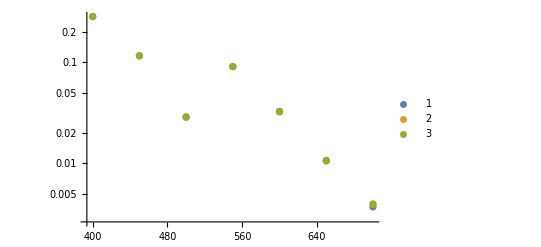

```mathematica
ListPlot[{Transpose[{lambdaRange,errorAbs[bck1000[[1]][[All,2]],eriQabsMie[[All,2]]]}],Transpose[{lambdaRange,errorAbs[bck2000[[1]][[All,2]],eriQabsMie[[All,2]]]}],Transpose[{lambdaRange,errorAbs[bck2500[[1]][[All,2]],eriQabsMie[[All,2]]]}]},ScalingFunctions->"Log",PlotLegends->Automatic]
```

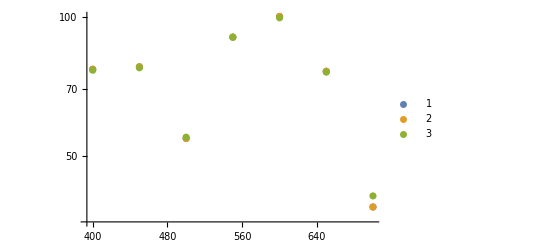

```mathematica
ListPlot[{Transpose[{lambdaRange,errorRel[bck1000[[1]][[All,2]],eriQabsMie[[All,2]]]}],Transpose[{lambdaRange,errorRel[bck1500[[1]][[All,2]],eriQabsMie[[All,2]]]}],Transpose[{lambdaRange,errorRel[bck2000[[1]][[All,2]],eriQabsMie[[All,2]]]}]},ScalingFunctions->"Log",PlotLegends->Automatic]
```

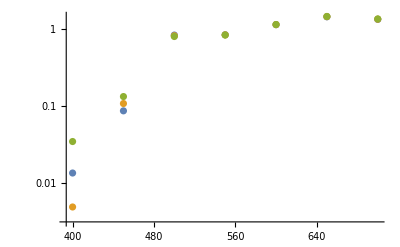

```mathematica
ListPlot[{Transpose[{lambdaRange,errorAbs[bck1500[[2]][[All,2]],eriQscaMie[[All,2]]]}],Transpose[{lambdaRange,errorAbs[bck2000[[2]][[All,2]],eriQscaMie[[All,2]]]}],Transpose[{lambdaRange,errorAbs[bck2500[[2]][[All,2]],eriQscaMie[[All,2]]]}]},ScalingFunctions->"Log",PlotRange->All]
```

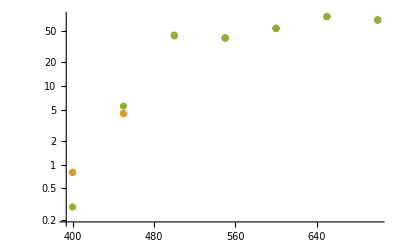

```mathematica
ListPlot[{Transpose[{lambdaRange,errorRel[bck1000[[2]][[All,2]],eriQscaMie[[All,2]]]}],Transpose[{lambdaRange,errorRel[bck1500[[2]][[All,2]],eriQscaMie[[All,2]]]}],Transpose[{lambdaRange,errorRel[bck2000[[2]][[All,2]],eriQscaMie[[All,2]]]}]},ScalingFunctions->"Log",PlotRange->All]
```

## PML

```mathematica
pml1000=importDataQ["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia\\PML\\1000.csv"];
pml1500=importDataQ["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia\\PML\\1500.csv"];
pml2000=importDataQ["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia\\PML\\2000.csv"];
pml2500=importDataQ["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia\\PML\\2500.csv"];
```

```mathematica
pmlBCK2000=importDataQ["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia\\PML_BCK_2000.csv"];
```

```mathematica
pmlBCK2000[[1]]
```

{{400,1.45813×10^7},{450,5.95217×10^6},{500,1.8209×10^6},{550,4.28091×10^6},{600,1.47043×10^6},{650,553468.},{700,299843.},{750,191972.},{800,138733.}}

```mathematica
Mean[errorAbs[pml1000[[1]][[All,2]],eriQabsMie[[All,2]]]]
Mean[errorAbs[pml1500[[1]][[All,2]],eriQabsMie[[All,2]]]]
Mean[errorAbs[pml2000[[1]][[All,2]],eriQabsMie[[All,2]]]]
Mean[errorAbs[pml2500[[1]][[All,2]],eriQabsMie[[All,2]]]]
```

0.0801659

0.0803932

0.0801458

0.0802124

```mathematica
Mean[errorAbs[pml1000[[2]][[All,2]],eriQscaMie[[All,2]]]]
Mean[errorAbs[pml1500[[2]][[All,2]],eriQscaMie[[All,2]]]]
Mean[errorAbs[pml2000[[2]][[All,2]],eriQscaMie[[All,2]]]]
Mean[errorAbs[pml2500[[2]][[All,2]],eriQscaMie[[All,2]]]]
```

0.805211

0.807146

0.809206

0.816287

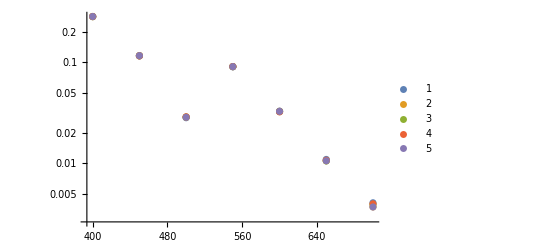

```mathematica
ListPlot[{Transpose[{lambdaRange,errorAbs[pml1000[[1]][[All,2]],eriQabsMie[[All,2]]]}],Transpose[{lambdaRange,errorAbs[pml1500[[1]][[All,2]],eriQabsMie[[All,2]]]}],Transpose[{lambdaRange,errorAbs[pml2000[[1]][[All,2]],eriQabsMie[[All,2]]]}],Transpose[{lambdaRange,errorAbs[pml2500[[1]][[All,2]],eriQabsMie[[All,2]]]}],
Transpose[{lambdaRange,errorAbs[pmlBCK2000[[1]][[All,2]],eriQabsMie[[All,2]]]}]},ScalingFunctions->"Log",PlotLegends->Automatic]
```

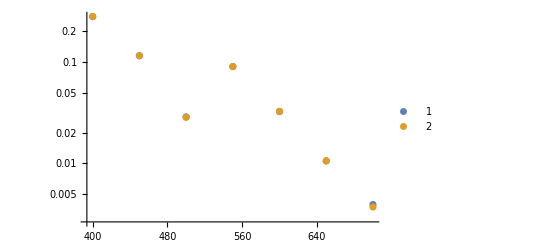

```mathematica
ListPlot[{Transpose[{lambdaRange,errorAbs[pml2000[[1]][[All,2]],eriQabsMie[[All,2]]]}],
Transpose[{lambdaRange,errorAbs[pmlBCK2000[[1]][[All,2]],eriQabsMie[[All,2]]]}]},ScalingFunctions->"Log",PlotLegends->Automatic]
```

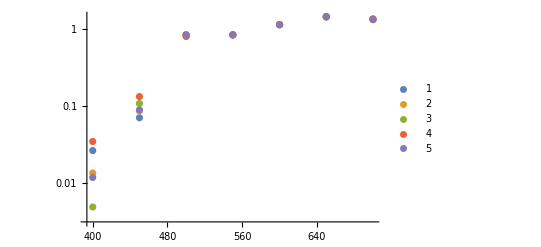

```mathematica
ListPlot[{Transpose[{lambdaRange,errorAbs[pml1000[[2]][[All,2]],eriQscaMie[[All,2]]]}],Transpose[{lambdaRange,errorAbs[pml1500[[2]][[All,2]],eriQscaMie[[All,2]]]}],Transpose[{lambdaRange,errorAbs[pml2000[[2]][[All,2]],eriQscaMie[[All,2]]]}],
Transpose[{lambdaRange,errorAbs[pml2500[[2]][[All,2]],eriQscaMie[[All,2]]]}],
Transpose[{lambdaRange,errorAbs[pmlBCK2000[[2]][[All,2]],eriQscaMie[[All,2]]]}]},ScalingFunctions->"Log",PlotRange->All,PlotLegends->Automatic]
```

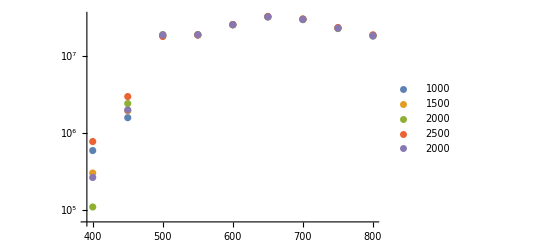

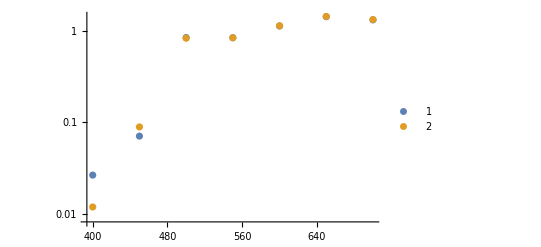

```mathematica
ListPlot[{Transpose[{lambdaRange,errorAbs[pml1000[[2]][[All,2]],eriQscaMie[[All,2]]]}],
Transpose[{lambdaRange,errorAbs[pmlBCK2000[[2]][[All,2]],eriQscaMie[[All,2]]]}]},ScalingFunctions->"Log",PlotRange->All,PlotLegends->Automatic]
```

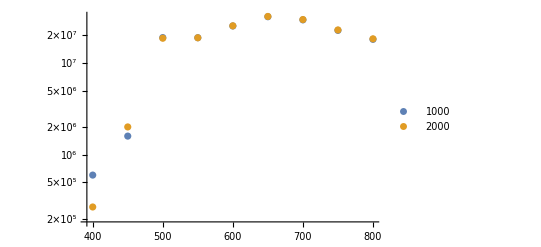

```mathematica
0.2418*h c/0.611821343
```

490.341

## Mesh

```mathematica
0.2418*h c/0.66620546222222
```

450.314

```mathematica
mesh150015002520=Import["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia\\Mesh\\1500_1500_25_20.csv"];
lambda0mesh150015002520=Range[700,400,-50];
lambda1mesh150015002520=Range[700,500,-50];
dataCabs0mesh150015002520=Drop[Drop[mesh150015002520[[All,2]],{1,3}],{8,17}]/(Pi*(2680)^2);
dataCabsmesh150015002520=Sort[Transpose[{lambda0mesh150015002520,dataCabs0mesh150015002520}]]
dataCsca0mesh150015002520=Drop[mesh150015002520[[All,2]],{1,15}]/(Pi*(2680)^2);
dataCscamesh1500150025200=Sort[Transpose[{lambda1mesh150015002520,dataCsca0mesh150015002520}]]
```

{{400,0.670151},{450,0.284396},{500,0.108743},{550,0.188632},{600,0.0614393},{650,0.024481},{700,0.0189341}}

{{500,1.53597},{550,1.65261},{600,1.95709},{650,2.25416},{700,2.51836}}

```mathematica
mesh150015002015=Import["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia\\Mesh\\1500_1500_20_15.csv"];
lambda0mesh150015002015=Range[700,400,-50];
lambda1mesh150015002015=Range[700,500,-50];
dataCabs0mesh150015002015=Drop[Drop[mesh150015002015[[All,2]],{1,3}],{8,17}]/(Pi*(2680)^2);
dataCabsmesh150015002015=Sort[Transpose[{lambda0mesh150015002015,dataCabs0mesh150015002015}]]
dataCsca0mesh150015002015=Drop[mesh150015002015[[All,2]],{1,15}]/(Pi*(2680)^2);
dataCscamesh1500150020150=Sort[Transpose[{lambda1mesh150015002015,dataCsca0mesh150015002015}]]
```

{{400,0.670151},{450,0.284396},{500,0.108743},{550,0.188632},{600,0.0614393},{650,0.024481},{700,0.0189341}}

{{500,1.53597},{550,1.65261},{600,1.95709},{650,2.25416},{700,2.51836}}

```mathematica
mesh15001500nolocal=Import["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia\\Mesh\\1500_1500_no_local.csv"];
lambda0mesh15001500nolocal=Range[700,400,-50];
lambda1mesh15001500nolocal=Range[700,500,-50];
dataCabs0mesh15001500nolocal=Drop[Drop[mesh15001500nolocal[[All,2]],{1,3}],{8,17}]/(Pi*(2680)^2);
dataCabsmesh15001500nolocal=Sort[Transpose[{lambda0mesh15001500nolocal,dataCabs0mesh15001500nolocal}]]
dataCsca0mesh15001500nolocal=Drop[mesh15001500nolocal[[All,2]],{1,15}]/(Pi*(2680)^2);
dataCscamesh15001500nolocal0=Sort[Transpose[{lambda1mesh15001500nolocal,dataCsca0mesh15001500nolocal}]]
```

{{400,0.669809},{450,0.284259},{500,0.108695},{550,0.188551},{600,0.0614007},{650,0.0244477},{700,0.0189088}}

{{500,1.53716},{550,1.65329},{600,1.956},{650,2.25344},{700,2.51845}}

```mathematica
dataCscamesh1500200020151=Transpose[{{400,450},{34652962.044491/(Pi*(2680)^2),37396871.024578/(Pi*(2680)^2)}}]
dataCscamesh1500200025201=Transpose[{{400,450},{34652962.044491/(Pi*(2680)^2),37396871.024578/(Pi*(2680)^2)}}]
dataCscamesh15002000nolocal1=Transpose[{{400,450},{34670770.635787/(Pi*(2680)^2),37406178.563308/(Pi*(2680)^2)}}]
```

{{400,1.53575},{450,1.65736}}

{{400,1.53575},{450,1.65736}}

{{400,1.53654},{450,1.65777}}

```mathematica
dataCscamesh150020002015=Join[dataCscamesh1500200020151,dataCscamesh1500150020150];
dataCscamesh150020002520=Join[dataCscamesh1500200025201,dataCscamesh1500150025200];
dataCscamesh15002000nolocal=Join[dataCscamesh15002000nolocal1,dataCscamesh15001500nolocal0];
```

# Datos bien

```mathematica
lambda=Range[400,600,4];
eriCabsMie=Table[{λ,mieQabs[nindexEriFit[λ],Sqrt[1.8235],2680,λ][[3]]},{λ,400,600,4}];
eriCscaMie=Table[{λ,mieQsca[nindexEriFit[λ],Sqrt[1.8235],2680,λ][[3]]},{λ,400,600,4}];
eriCextMie=Table[{λ,mieQext[nindexEriFit[λ],Sqrt[1.8235],2680,λ][[3]]},{λ,400,600,4}];
eriQabsMie=Table[{λ,mieQabs[nindexEriFit[λ],Sqrt[1.8235],2680,λ][[4]]},{λ,400,600,4}];
eriQscaMie=Table[{λ,mieQsca[nindexEriFit[λ],Sqrt[1.8235],2680,λ][[4]]},{λ,400,600,4}];
eriQextMie=Table[{λ,mieQext[nindexEriFit[λ],Sqrt[1.8235],2680,λ][[4]]},{λ,400,600,4}];
```

```mathematica
interpCabsMie=Interpolation[eriCabsMie];
```

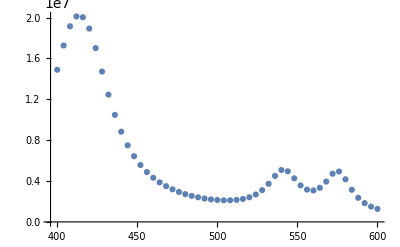

```mathematica
ListPlot[eriCabsMie]
```

```mathematica
FindMaximum[interpCabsMie[x],{x,400,430}]
FindMaximum[interpCabsMie[x],{x,530,550}]
FindMaximum[interpCabsMie[x],{x,560,580}]
```

{2.02024×10^7,{x→413.694}}

{5.10856×10^6,{x→541.213}}

{4.95125×10^6,{x→575.116}}

## PML

```mathematica
dataQext[dataCabs_,dataCsca_]:=Module[{dataCext},
dataCext=Transpose[{dataCabs[[All,1]],dataCabs[[All,2]]+dataCsca[[All,2]]}]]
```

```mathematica
dataPML=Import["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia_0\\PML.csv"];
dataPMLCsca=Import["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia_0\\PML_Ccsa.csv"];

dataCabsPML500=Transpose[{dataPML[[All,1]],dataPML[[All,2]]/(Pi*2680^2)}];
dataCabsPML1000=Transpose[{dataPML[[All,1]],dataPML[[All,3]]/(Pi*2680^2)}];
dataCabsPML1100=Transpose[{dataPML[[All,1]],dataPML[[All,4]]/(Pi*2680^2)}];
dataCabsPML1250=Transpose[{dataPML[[All,1]],dataPML[[All,5]]/(Pi*2680^2)}];
dataCabsPML1340=Transpose[{dataPML[[All,1]],dataPML[[All,6]]/(Pi*2680^2)}];
dataCabsPML1470=Transpose[{dataPML[[All,1]],dataPML[[All,7]]/(Pi*2680^2)}];
dataCabsPML1500=Transpose[{dataPML[[All,1]],dataPML[[All,8]]/(Pi*2680^2)}];
dataCabsPML2000=Transpose[{dataPML[[All,1]],dataPML[[All,9]]/(Pi*2680^2)}];
dataCabsPML3000=Transpose[{dataPML[[All,1]],dataPML[[All,10]]/(Pi*2680^2)}];
```

```mathematica
dataCscaPML500=Transpose[{dataPML[[All,1]],dataPMLCsca[[All,2]]/(Pi*2680^2)}];
dataCscaPML1000=Transpose[{dataPML[[All,1]],dataPMLCsca[[All,3]]/(Pi*2680^2)}];
dataCscaPML1100=Transpose[{dataPML[[All,1]],dataPMLCsca[[All,4]]/(Pi*2680^2)}];
dataCscaPML1250=Transpose[{dataPML[[All,1]],dataPMLCsca[[All,5]]/(Pi*2680^2)}];
dataCscaPML1340=Transpose[{dataPML[[All,1]],dataPMLCsca[[All,6]]/(Pi*2680^2)}];
dataCscaPML1470=Transpose[{dataPML[[All,1]],dataPMLCsca[[All,7]]/(Pi*2680^2)}];
dataCscaPML1500=Transpose[{dataPML[[All,1]],dataPMLCsca[[All,8]]/(Pi*2680^2)}];
dataCscaPML2000=Transpose[{dataPML[[All,1]],dataPMLCsca[[All,9]]/(Pi*2680^2)}];
dataCscaPML3000=Transpose[{dataPML[[All,1]],dataPMLCsca[[All,10]]/(Pi*2680^2)}];
```

```mathematica
eriQabsMie2=Table[{λ,mieQabs[nindexEriFit[λ],Sqrt[1.8235],2680,λ][[4]]},{λ,dataPML[[All,1]]}];
eriQscaMie2=Table[{λ,mieQsca[nindexEriFit[λ],Sqrt[1.8235],2680,λ][[4]]},{λ,dataPML[[All,1]]}];
eriQextMie2=Table[{λ,mieQext[nindexEriFit[λ],Sqrt[1.8235],2680,λ][[4]]},{λ,dataPML[[All,1]]}];
```

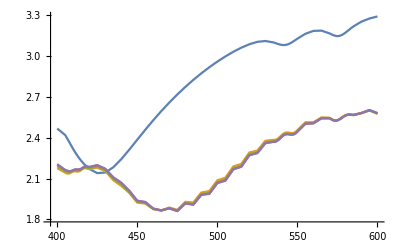

```mathematica
ListLinePlot[{eriQextMie2,dataQext[dataCabsPML500,dataCscaPML500],dataQext[dataCabsPML1000,dataCscaPML1000],dataQext[dataCabsPML1340,dataCscaPML1340],dataQext[dataCabsPML1470,dataCscaPML1470]}]
```

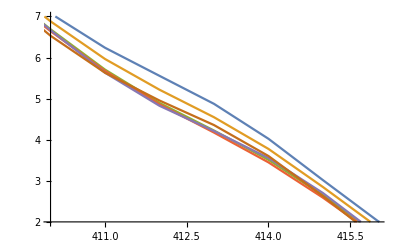

```mathematica
ListLinePlot[{Transpose[{dataPML[[All,1]],errorRel[dataQext[dataCabsPML500,dataCscaPML500][[All,2]],eriQextMie2[[All,2]]]}],Transpose[{dataPML[[All,1]],errorRel[dataQext[dataCabsPML1000,dataCscaPML1000][[All,2]],eriQextMie2[[All,2]]]}],Transpose[{dataPML[[All,1]],errorRel[dataQext[dataCabsPML1340,dataCscaPML1340][[All,2]],eriQextMie2[[All,2]]]}],
Transpose[{dataPML[[All,1]],errorRel[dataQext[dataCabsPML1470,dataCscaPML1470][[All,2]],eriQextMie2[[All,2]]]}],
Transpose[{dataPML[[All,1]],errorRel[dataQext[dataCabsPML2000,dataCscaPML2000][[All,2]],eriQextMie2[[All,2]]]}],
Transpose[{dataPML[[All,1]],errorRel[dataQext[dataCabsPML3000,dataCscaPML3000][[All,2]],eriQextMie2[[All,2]]]}]},PlotRange->{{410,416},{2,7}}]
```

```mathematica
Length[dataPML[[All,1]]]
```

77

```mathematica
Mean[Drop[Drop[errorRel[dataQext[dataCabsPML500,dataCscaPML500][[All,2]],eriQextMie2[[All,2]]],7],-60]]
Mean[Drop[Drop[errorRel[dataQext[dataCabsPML1000,dataCscaPML1000][[All,2]],eriQextMie2[[All,2]]],7],-60]]
Mean[Drop[Drop[errorRel[dataQext[dataCabsPML2000,dataCscaPML2000][[All,2]],eriQextMie2[[All,2]]],7],-60]]
```

2.82464

2.60545

2.43132

```mathematica
Mean[Drop[Drop[errorRel[dataQext[dataCabsPML500,dataCscaPML500][[All,2]],eriQextMie2[[All,2]]],49],-3]]
Mean[Drop[Drop[errorRel[dataQext[dataCabsPML1000,dataCscaPML1000][[All,2]],eriQextMie2[[All,2]]],49],-3]]
Mean[Drop[Drop[errorRel[dataQext[dataCabsPML2000,dataCscaPML2000][[All,2]],eriQextMie2[[All,2]]],49],-3]]
```

20.0851

20.2491

20.2687

```mathematica
Mean[Drop[Drop[errorRel[dataQext[dataCabsPML500,dataCscaPML500][[All,2]],eriQextMie2[[All,2]]],43],-27]]
Mean[Drop[Drop[errorRel[dataQext[dataCabsPML1000,dataCscaPML1000][[All,2]],eriQextMie2[[All,2]]],43],-27]]
Mean[Drop[Drop[errorRel[dataQext[dataCabsPML2000,dataCscaPML2000][[All,2]],eriQextMie2[[All,2]]],43],-27]]
```

21.2202

21.5238

21.6621

```mathematica
Drop[Drop[errorRel[dataQext[dataCabsPML500,dataCscaPML500][[All,2]],eriQextMie2[[All,2]]],43],-27]
```

{21.9754,21.5387,21.1699,20.9328,20.8588,20.9388,21.1272}

```mathematica
Transpose[{dataPML[[All,1]],errorRel[dataQext[dataCabsPML500,dataCscaPML500][[All,2]],eriQextMie2[[All,2]]]}]
```

{{400,11.7945},{405,11.379},{406,10.8969},{407,10.1792},{408,9.22394},{409,8.11011},{410,7.07377},{411,6.23829},{412,5.55444},{413,4.873},{414,4.02239},{415,3.01594},{416,2.02757},{417,1.25042},{418,0.756671},{419,0.434495},{420,0.0731417},{425,1.88772},{430,0.528569},{435,4.31042},{440,8.72047},{445,13.7004},{450,19.3562},{455,22.0065},{460,25.7428},{465,28.077},{470,28.9665},{475,31.1287},{480,30.3793},{485,31.821},{490,30.4284},{495,31.1186},{500,29.4252},{505,29.6774},{510,27.7408},{515,27.8423},{520,25.7178},{525,25.6971},{530,23.5323},{535,23.0584},{536,22.967},{537,22.7469},{538,22.4018},{539,21.9754},{540,21.5387},{541,21.1699},{542,20.9328},{543,20.8588},{544,20.9388},{545,21.1272},{546,21.3549},{547,21.5477},{548,21.6459},{549,21.6182},{550,21.4683},{555,20.5116},{560,21.0439},{565,19.9723},{570,19.5269},{571,19.6182},{572,19.6915},{573,19.7143},{574,19.6702},{575,19.5621},{576,19.4108},{577,19.2493},{578,19.115},{579,19.0422},{580,19.0543},{581,19.1603},{582,19.3524},{583,19.6078},{584,19.8931},{585,20.1702},{590,20.6058},{595,20.5376},{600,21.6881}}

```mathematica
Mean[errorRel[dataQext[dataCabsPML500,dataCscaPML500][[All,2]],eriQextMie2[[All,2]]]]
Mean[errorRel[dataQext[dataCabsPML1000,dataCscaPML1000][[All,2]],eriQextMie2[[All,2]]]]
Mean[errorRel[dataQext[dataCabsPML1340,dataCscaPML1340][[All,2]],eriQextMie2[[All,2]]]]
Mean[errorRel[dataQext[dataCabsPML1470,dataCscaPML1470][[All,2]],eriQextMie2[[All,2]]]]
Mean[errorRel[dataQext[dataCabsPML2000,dataCscaPML2000][[All,2]],eriQextMie2[[All,2]]]]
Mean[errorRel[dataQext[dataCabsPML3000,dataCscaPML3000][[All,2]],eriQextMie2[[All,2]]]]
```

17.8995

17.9874

17.9617

17.959

17.9755

18.0952

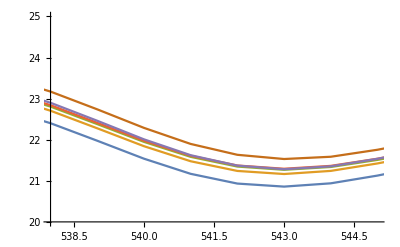

```mathematica
ListLinePlot[{Transpose[{dataPML[[All,1]],errorRel[dataQext[dataCabsPML500,dataCscaPML500][[All,2]],eriQextMie2[[All,2]]]}],Transpose[{dataPML[[All,1]],errorRel[dataQext[dataCabsPML1000,dataCscaPML1000][[All,2]],eriQextMie2[[All,2]]]}],Transpose[{dataPML[[All,1]],errorRel[dataQext[dataCabsPML1340,dataCscaPML1340][[All,2]],eriQextMie2[[All,2]]]}],
Transpose[{dataPML[[All,1]],errorRel[dataQext[dataCabsPML1470,dataCscaPML1470][[All,2]],eriQextMie2[[All,2]]]}],
Transpose[{dataPML[[All,1]],errorRel[dataQext[dataCabsPML2000,dataCscaPML2000][[All,2]],eriQextMie2[[All,2]]]}],
Transpose[{dataPML[[All,1]],errorRel[dataQext[dataCabsPML3000,dataCscaPML3000][[All,2]],eriQextMie2[[All,2]]]}]},PlotRange->{{538,545},{20,25}}]
```

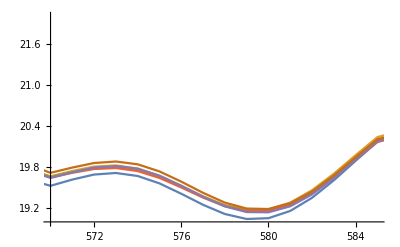

```mathematica
ListLinePlot[{Transpose[{dataPML[[All,1]],errorRel[dataQext[dataCabsPML500,dataCscaPML500][[All,2]],eriQextMie2[[All,2]]]}],Transpose[{dataPML[[All,1]],errorRel[dataQext[dataCabsPML1000,dataCscaPML1000][[All,2]],eriQextMie2[[All,2]]]}],Transpose[{dataPML[[All,1]],errorRel[dataQext[dataCabsPML1340,dataCscaPML1340][[All,2]],eriQextMie2[[All,2]]]}],
Transpose[{dataPML[[All,1]],errorRel[dataQext[dataCabsPML1470,dataCscaPML1470][[All,2]],eriQextMie2[[All,2]]]}],
Transpose[{dataPML[[All,1]],errorRel[dataQext[dataCabsPML2000,dataCscaPML2000][[All,2]],eriQextMie2[[All,2]]]}],
Transpose[{dataPML[[All,1]],errorRel[dataQext[dataCabsPML3000,dataCscaPML3000][[All,2]],eriQextMie2[[All,2]]]}]},PlotRange->{{570,585},{19,22}}]
```

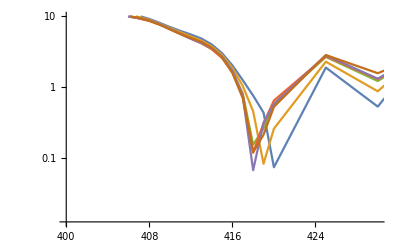

```mathematica
ListLinePlot[{Transpose[{dataPML[[All,1]],errorRel[dataQext[dataCabsPML500,dataCscaPML500][[All,2]],eriQextMie2[[All,2]]]}],Transpose[{dataPML[[All,1]],errorRel[dataQext[dataCabsPML1000,dataCscaPML1000][[All,2]],eriQextMie2[[All,2]]]}],Transpose[{dataPML[[All,1]],errorRel[dataQext[dataCabsPML1340,dataCscaPML1340][[All,2]],eriQextMie2[[All,2]]]}],
Transpose[{dataPML[[All,1]],errorRel[dataQext[dataCabsPML1470,dataCscaPML1470][[All,2]],eriQextMie2[[All,2]]]}],
Transpose[{dataPML[[All,1]],errorRel[dataQext[dataCabsPML2000,dataCscaPML2000][[All,2]],eriQextMie2[[All,2]]]}],
Transpose[{dataPML[[All,1]],errorRel[dataQext[dataCabsPML3000,dataCscaPML3000][[All,2]],eriQextMie2[[All,2]]]}]},PlotRange->{{400,430},{0,10}},ScalingFunctions->"Log"]
```

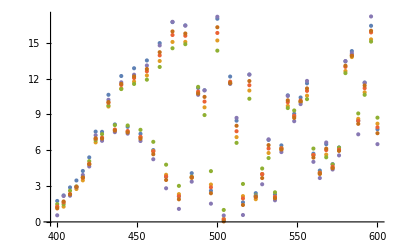

```mathematica
ListPlot[{Transpose[{lambda,errorRel[dataCabsPML500[[All,2]],eriCabsMie[[All,2]]]}],Transpose[{lambda,errorRel[dataCabsPML1000[[All,2]],eriCabsMie[[All,2]]]}],Transpose[{lambda,errorRel[dataCabsPML1500[[All,2]],eriCabsMie[[All,2]]]}],Transpose[{lambda,errorRel[dataCabsPML2000[[All,2]],eriCabsMie[[All,2]]]}],
Transpose[{lambda,errorRel[dataCabsPML2500[[All,2]],eriCabsMie[[All,2]]]}],
Transpose[{lambda,errorRel[dataCabsPML3000[[All,2]],eriCabsMie[[All,2]]]}]},PlotRange->All]
```

## Mesh

```mathematica
dataMeshCabs=Import["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia_0\\\Local Mesh\Cabs.csv"];
dataMeshCsca=Import["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Pruebas\\Convergencia_0\\Local Mesh\\Csca.csv"];

dataCabsMesh7=Transpose[{dataMeshCabs[[All,1]],dataMeshCabs[[All,2]]/(Pi*(2680^2))}];
dataCabsMesh10=Transpose[{dataMeshCabs[[All,1]],dataMeshCabs[[All,3]]/(Pi*(2680^2))}];
dataCabsMesh12=Transpose[{dataMeshCabs[[All,1]],dataMeshCabs[[All,4]]/(Pi*(2680^2))}];
dataCabsMesh15=Transpose[{dataMeshCabs[[All,1]],dataMeshCabs[[All,5]]/(Pi*(2680^2))}];
dataCabsMesh17=Transpose[{dataMeshCabs[[All,1]],dataMeshCabs[[All,6]]/(Pi*(2680^2))}];

dataCscaMesh7=Transpose[{dataMeshCsca[[All,1]],dataMeshCsca[[All,2]]/(Pi*(2680^2))}];
dataCscaMesh10=Transpose[{dataMeshCsca[[All,1]],dataMeshCsca[[All,3]]/(Pi*(2680^2))}];
dataCscaMesh12=Transpose[{dataMeshCsca[[All,1]],dataMeshCsca[[All,4]]/(Pi*(2680^2))}];
dataCscaMesh15=Transpose[{dataMeshCsca[[All,1]],dataMeshCsca[[All,5]]/(Pi*(2680^2))}];
dataCscaMesh17=Transpose[{dataMeshCsca[[All,1]],dataMeshCsca[[All,6]]/(Pi*(2680^2))}];
```

```mathematica
eriQabsMieMesh=Table[{λ,mieQabs[nindexEriFit[λ],Sqrt[1.8235],2680,λ][[4]]},{λ,dataMeshCabs[[All,1]]}];
eriQscaMieMesh=Table[{λ,mieQsca[nindexEriFit[λ],Sqrt[1.8235],2680,λ][[4]]},{λ,dataMeshCsca[[All,1]]}];
```

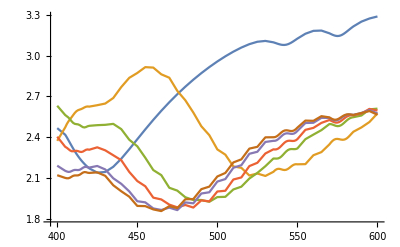

```mathematica
ListLinePlot[{eriQextMie2,dataQext[dataCabsMesh7,dataCscaMesh7],dataQext[dataCabsMesh10,dataCscaMesh10],dataQext[dataCabsMesh12,dataCscaMesh12],dataQext[dataCabsMesh15,dataCscaMesh15],dataQext[dataCabsMesh17,dataCscaMesh17]},PlotRange->All]
```

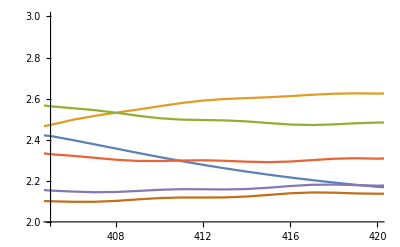

```mathematica
ListLinePlot[{eriQextMie2,dataQext[dataCabsMesh7,dataCscaMesh7],dataQext[dataCabsMesh10,dataCscaMesh10],dataQext[dataCabsMesh12,dataCscaMesh12],dataQext[dataCabsMesh15,dataCscaMesh15],dataQext[dataCabsMesh17,dataCscaMesh17]},PlotRange->{{405,420},{2,3}}]
```

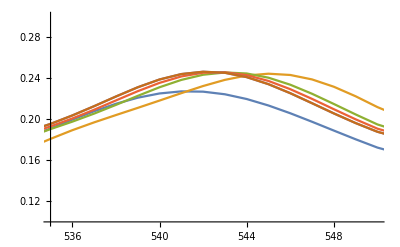

```mathematica
ListLinePlot[{eriQabsMieMesh,dataCabsMesh7,dataCabsMesh10,dataCabsMesh12,dataCabsMesh15,dataCabsMesh17},PlotRange->{{535,550},{0.1,0.3}}]
```

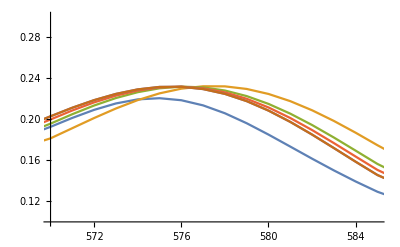

```mathematica
ListLinePlot[{eriQabsMieMesh,dataCabsMesh7,dataCabsMesh10,dataCabsMesh12,dataCabsMesh15,dataCabsMesh17},PlotRange->{{570,585},{0.1,0.3}}]
```

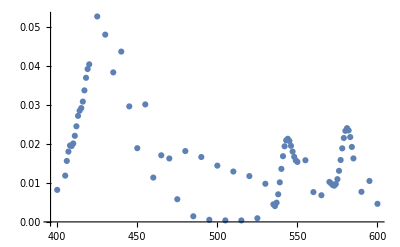

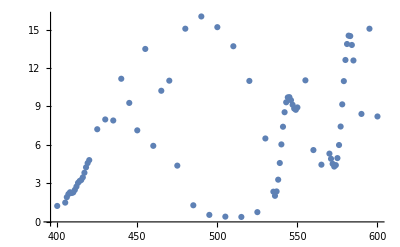

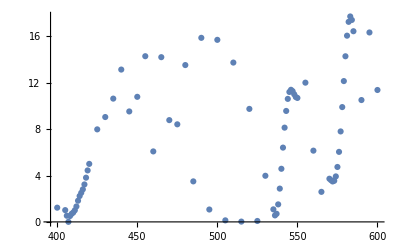

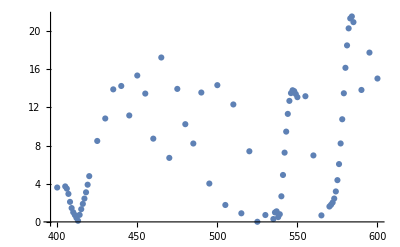

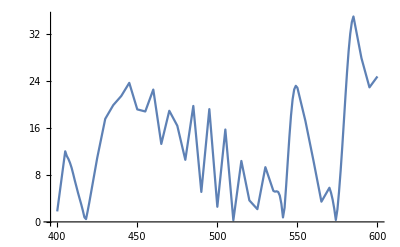

```mathematica
ListPlot[{Transpose[{dataCabsMesh17[[All,1]],errorAbs[dataCabsMesh17[[All,2]],eriQabsMieMesh[[All,2]]]}]},PlotRange->All]
ListPlot[{Transpose[{dataCabsMesh15[[All,1]],errorRel[dataCabsMesh15[[All,2]],eriQabsMieMesh[[All,2]]]}]},PlotRange->All]
ListPlot[{Transpose[{dataCabsMesh12[[All,1]],errorRel[dataCabsMesh12[[All,2]],eriQabsMieMesh[[All,2]]]}]},PlotRange->All]
ListPlot[{Transpose[{dataCabsMesh10[[All,1]],errorRel[dataCabsMesh10[[All,2]],eriQabsMieMesh[[All,2]]]}]},PlotRange->All]
ListLinePlot[{Transpose[{dataCabsMesh7[[All,1]],errorRel[dataCabsMesh7[[All,2]],eriQabsMieMesh[[All,2]]]}]},PlotRange->All]
```

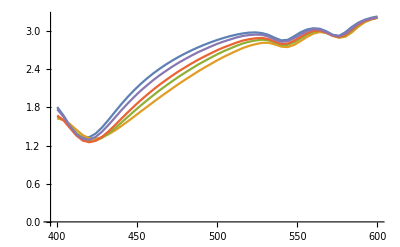

```mathematica
ListLinePlot[{eriQscaMie,dataCscaLocalMesh2520,dataCscaLocalMesh2015,dataCscaLocalMesh1510,dataCscaLocalMesh107},PlotRange->All]
```

```mathematica
(1.386471835872126-1.3779143880269906)/1.3779143880269906
```

0.00621044

```mathematica
eriQscaMie
dataCscaLocalMesh107
```

```mathematica
(2.8545177525645538-2.8332054766949604)/2.8332054766949604
```

0.00752232

## Local Mesh

```mathematica
dataLocalCabs=Import["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia_0\\Local_mesh\\Cabs.csv"];
dataLocalCsca=Import["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia_0\\Local_mesh\\Csca.csv"];

dataCabsLocalMesh2520=Transpose[{dataLocalCabs[[All,1]],dataLocalCabs[[All,2]]/(Pi*(2680^2))}];
dataCabsLocalMesh1613=Transpose[{dataLocalCabs[[All,1]],dataLocalCabs[[All,3]]/(Pi*(2680^2))}];
dataCabsLocalMesh1510=Transpose[{dataLocalCabs[[All,1]],dataLocalCabs[[All,4]]/(Pi*(2680^2))}];
dataCabsLocalMesh107=Transpose[{dataLocalCabs[[All,1]],dataLocalCabs[[All,5]]/(Pi*(2680^2))}];

dataCscaLocalMesh2520=Transpose[{dataLocalCsca[[All,1]],dataLocalCsca[[All,2]]/(Pi*(2680^2))}];
dataCscaLocalMesh1613=Transpose[{dataLocalCabs[[All,1]],dataLocalCsca[[All,3]]/(Pi*(2680^2))}];
dataCscaLocalMesh1510=Transpose[{dataLocalCsca[[All,1]],dataLocalCsca[[All,4]]/(Pi*(2680^2))}];
dataCscaLocalMesh107=Transpose[{dataLocalCsca[[All,1]],dataLocalCsca[[All,5]]/(Pi*(2680^2))}];
```

```mathematica
eriQextMieLocalMesh=Table[{λ,mieQext[nindexEriFit[λ],Sqrt[1.8235],2680,λ][[4]]},{λ,dataLocalCsca[[All,1]]}];
```

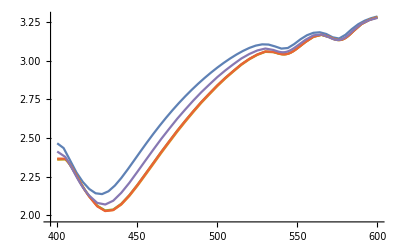

```mathematica
ListLinePlot[{eriQextMie,dataQext[dataCabsLocalMesh2520,dataCscaLocalMesh2520],dataQext[dataCabsLocalMesh1613,dataCscaLocalMesh1613],dataQext[dataCabsLocalMesh1510,dataCscaLocalMesh1510],dataQext[dataCabsLocalMesh107,dataCscaLocalMesh107]},PlotRange->All]
```

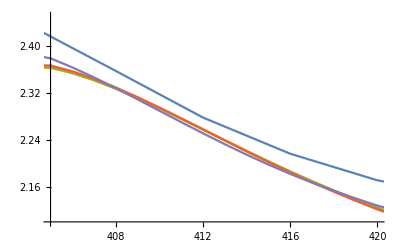

```mathematica
ListLinePlot[{eriQextMie,dataQext[dataCabsLocalMesh2520,dataCscaLocalMesh2520],dataQext[dataCabsLocalMesh1613,dataCscaLocalMesh1613],dataQext[dataCabsLocalMesh1510,dataCscaLocalMesh1510],dataQext[dataCabsLocalMesh107,dataCscaLocalMesh107]},PlotRange->{{405,420},{2.1,2.45}}]
```

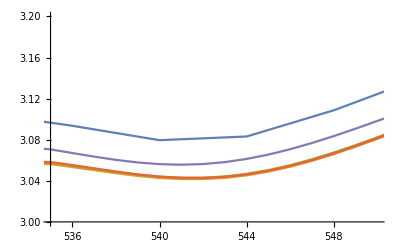

```mathematica
ListLinePlot[{eriQextMie,dataQext[dataCabsLocalMesh2520,dataCscaLocalMesh2520],dataQext[dataCabsLocalMesh1613,dataCscaLocalMesh1613],dataQext[dataCabsLocalMesh1510,dataCscaLocalMesh1510],dataQext[dataCabsLocalMesh107,dataCscaLocalMesh107]},PlotRange->{{535,550},{3,3.2}}]
```

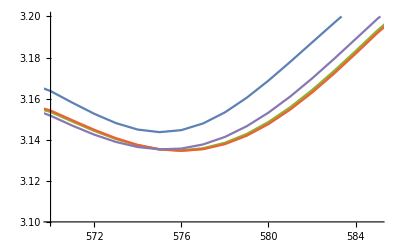

```mathematica
ListLinePlot[{eriQextMieLocalMesh,dataQext[dataCabsLocalMesh2520,dataCscaLocalMesh2520],dataQext[dataCabsLocalMesh1613,dataCscaLocalMesh1613],dataQext[dataCabsLocalMesh1510,dataCscaLocalMesh1510],dataQext[dataCabsLocalMesh107,dataCscaLocalMesh107]},PlotRange->{{570,585},{3.1,3.2}}]
```

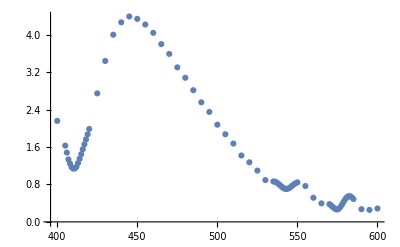

```mathematica
ListPlot[{Transpose[{dataCabsLocalMesh107[[All,1]],errorRel[dataQext[dataCabsLocalMesh107,dataCscaLocalMesh107][[All,2]],eriQextMieLocalMesh[[All,2]]]}]},PlotRange->All]
```

```mathematica
ListLinePlot[{eriQscaMie,dataCscaLocalMesh2520,dataCscaLocalMesh2015,dataCscaLocalMesh1510,dataCscaLocalMesh107},PlotRange->All]
```

-Graphics-

```mathematica
(1.386471835872126-1.3779143880269906)/1.3779143880269906
```

0.00621044

```mathematica
eriQscaMie
dataCscaLocalMesh107
```

```mathematica
(2.8545177525645538-2.8332054766949604)/2.8332054766949604
```

0.00752232